# Classical Machine Learning

```mathematica
oxyDataReducedYes = Thread[Table[reducedOxyYes80[[x,All,All]],{x,Length[reducedOxyYes80]}]-> "Yes"];
oxyDataReducedNo = Thread[Table[reducedOxyNo80[[x,All,All]],{x,Length[reducedOxyNo80]}]->"No"];

reducedDataYesAndNo = Join[oxyDataReducedYes,oxyDataReducedNo];
```

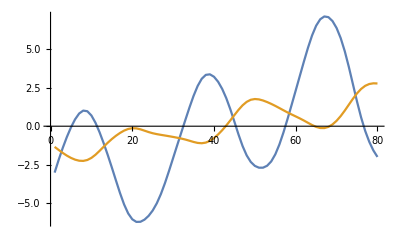

```mathematica
ListLinePlot[reducedDataYesAndNo[[1]]]
```

```mathematica
Values[reducedDataYesAndNo[[1]]]
```

Yes

```mathematica
dataPoints = Length[reducedDataYesAndNo];
fracTrainTest = 0.8;
trainPoints = Round@dataPoints*fracTrainTest;
testPoints = dataPoints-trainPoints;

trainDataYesAndNo = RandomSample[reducedDataYesAndNo,trainPoints];
testDataYesAndNo = Complement[reducedDataYesAndNo,trainDataYesAndNo];

Counts[Table[Values@trainDataYesAndNo[[n]],{n,trainPoints}]]
Counts[Table[Values@testDataYesAndNo[[n]],{n,testPoints}]]
```

<|Yes→22,No→26|>

<|Yes→8,No→4|>

```mathematica
classOnReduced = Classify[trainDataYesAndNo]
```

ClassifierFunction[…]

```mathematica
ClassifierMeasurements[classOnReduced,testDataYesAndNo, "Accuracy"]
```

0.75